```mathematica
Integrate[(ψN r/rN Exp[1-r/rN])^2,{r,rN,Infinity},Assumptions->rN>0]
```

(5 rN ψN^2)/4

```mathematica
Integrate[(x Exp[1-x])^2,{x,1,Infinity}]
```

5/4

```mathematica
Normal[Series[(D r+C r^2+B r^3+A r^4)^2,{r,0,8}]]
```

D^2 r^2+2 C D r^3+(C^2+2 B D) r^4+(2 B C+2 A D) r^5+(B^2+2 A C) r^6+2 A B r^7+A^2 r^8

```mathematica
Integrate[Normal[Series[(D r+C r^2+B r^3+A r^4)^2,{r,0,8}]],{r,0,h}]
```

(D^2 h^3)/3+1/2 C D h^4+(C^2 h^5)/5+2/5 B D h^5+1/3 B C h^6+1/3 A D h^6+(B^2 h^7)/7+2/7 A C h^7+1/4 A B h^8+(A^2 h^9)/9

```mathematica
(* 2024.05.02 ContEvol H failure.nb *)
T0mat[h_]={{-2/h^3,1/h^2,1/h^2},
{3/h^2,-2/h,-1/h},
{0,1,0}};
Tmat[i_,h_]={{(-1+2 i)/(h^4 i^2),(-3-2 i)/(h^4 (1+i)^2),1/(h^3 i),1/(h^3 (1+i))},
{(2-6 i^2)/(h^3 i^2),(2 (2+6 i+3 i^2))/(h^3 (1+i)^2),-(2+3 i)/(h^2 i),(-1-3 i)/(h^2 (1+i))},
{((1+i) (-1-3 i+6 i^2))/(h^2 i^2),-(i (8+15 i+6 i^2))/(h^2 (1+i)^2),((1+i) (1+3 i))/(h i),(i (2+3 i))/(h (1+i))},
{-(2 (-1+i) (1+i)^2)/(h i),(2 i^2 (2+i))/(h (1+i)),-(1+i)^2,-i^2}};
```

```mathematica
Pbar[i_,h_]:={{-2/9 h^9 i^9+2/9 h^9 (1+i)^9,1/4 (-h^8 i^8+h^8 (1+i)^8),2/7 (-h^7 i^7+h^7 (1+i)^7),1/3 (-h^6 i^6+h^6 (1+i)^6)},
{1/4 (-h^8 i^8+h^8 (1+i)^8),2/7 (-h^7 i^7+h^7 (1+i)^7),1/3 (-h^6 i^6+h^6 (1+i)^6),2/5 (-h^5 i^5+h^5 (1+i)^5)},
{2/7 (-h^7 i^7+h^7 (1+i)^7),1/3 (-h^6 i^6+h^6 (1+i)^6),2/5 (-h^5 i^5+h^5 (1+i)^5),1/2 (-h^4 i^4+h^4 (1+i)^4)},
{1/3 (-h^6 i^6+h^6 (1+i)^6),2/5 (-h^5 i^5+h^5 (1+i)^5),1/2 (-h^4 i^4+h^4 (1+i)^4),2/3 (-h^3 i^3+h^3 (1+i)^3)}};
Qbar[i_,h_]:={{24/7 (-h^7 i^7+h^7 (1+i)^7)+1/2 (-h^8 i^8+h^8 (1+i)^8),2 (-h^6 i^6+h^6 (1+i)^6)+4/7 (-h^7 i^7+h^7 (1+i)^7),4/5 (-h^5 i^5+h^5 (1+i)^5)+2/3 (-h^6 i^6+h^6 (1+i)^6),4/5 (-h^5 i^5+h^5 (1+i)^5)},
{4 (-h^6 i^6+h^6 (1+i)^6)+4/7 (-h^7 i^7+h^7 (1+i)^7),12/5 (-h^5 i^5+h^5 (1+i)^5)+2/3 (-h^6 i^6+h^6 (1+i)^6),-h^4 i^4+h^4 (1+i)^4+4/5 (-h^5 i^5+h^5 (1+i)^5),-h^4 i^4+h^4 (1+i)^4},
{24/5 (-h^5 i^5+h^5 (1+i)^5)+2/3 (-h^6 i^6+h^6 (1+i)^6),3 (-h^4 i^4+h^4 (1+i)^4)+4/5 (-h^5 i^5+h^5 (1+i)^5),-h^4 i^4+h^4 (1+i)^4+4/3 (-h^3 i^3+h^3 (1+i)^3),4/3 (-h^3 i^3+h^3 (1+i)^3)},
{6 (-h^4 i^4+h^4 (1+i)^4)+4/5 (-h^5 i^5+h^5 (1+i)^5),-h^4 i^4+h^4 (1+i)^4+4 (-h^3 i^3+h^3 (1+i)^3),2 (-h^2 i^2+h^2 (1+i)^2)+4/3 (-h^3 i^3+h^3 (1+i)^3),2 (-h^2 i^2+h^2 (1+i)^2)}};
```

```mathematica
(* N = 1, h = 1 case *)
ψq[r_]:=D r+C r^2+B r^3;
ψdotq[r_]:=D+2 C r+3 B r^2;
```

```mathematica
ψtail[r_]:=ψN r Exp[1-r];
ϕtail[r_]:=ϕN r Exp[1-r];
```

```mathematica
Series[Solve[ψdotq[0]==ψdot0&&ψq[1]==ψh&&ψdotq[1]==ψdoth,{B,C,D}],{h,0,0}]
```

{{B→ψdot0+ψdoth-2 ψh,C→-2 ψdot0-ψdoth+3 ψh,D→ψdot0}}

```mathematica
ψψq[r_]:=ψdot0 r+(-2 ψdot0-ψdoth+3 ψh) r^2+(ψdot0+ψdoth-2 ψh) r^3;
ϕϕq[r_]:=ϕdot0 r+(-2 ϕdot0-ϕdoth+3 ϕh) r^2+(ϕdot0+ϕdoth-2 ϕh) r^3;
```

```mathematica
Integrate[Simplify[D[D[ψψq[r], r], r]+2ψψq[r]/r+ϕϕq[r]]^2,{r,0,1}]+Integrate[(D[D[ψtail[r], r], r]+2ψtail[r]/r+ϕtail[r])^2,{r,1,Infinity}]
```

ϕdot0^2/105-(ϕdot0 ϕdoth)/70+ϕdoth^2/105+(13 ϕdot0 ϕh)/210-(11 ϕdoth ϕh)/105+(13 ϕh^2)/35-(2 ϕdot0 ψdot0)/15+(7 ϕh ψdot0)/15+(22 ψdot0^2)/15-(ϕdoth ψdoth)/5+(28 ϕh ψdoth)/15+(18 ψdot0 ψdoth)/5+(52 ψdoth^2)/15+(7 ϕdot0 ψh)/15-(2 ϕdoth ψh)/15-(ϕh ψh)/3-(118 ψdot0 ψh)/15-(118 ψdoth ψh)/15+(56 ψh^2)/5+5/4 (ϕN+ψN)^2

```mathematica
ϵ[ψh_,ψdot0_,ψdoth_,ϕh_,ϕdot0_,ϕdoth_]:=ϕdot0^2/105-(ϕdot0 ϕdoth)/70+ϕdoth^2/105+(13 ϕdot0 ϕh)/210-(11 ϕdoth ϕh)/105+(13 ϕh^2)/35-(2 ϕdot0 ψdot0)/15+(7 ϕh ψdot0)/15+(22 ψdot0^2)/15-(ϕdoth ψdoth)/5+(28 ϕh ψdoth)/15+(18 ψdot0 ψdoth)/5+(52 ψdoth^2)/15+(7 ϕdot0 ψh)/15-(2 ϕdoth ψh)/15-(ϕh ψh)/3-(118 ψdot0 ψh)/15-(118 ψdoth ψh)/15+(56 ψh^2)/5+5/4 (ϕh+ψh)^2;
```

```mathematica
D[ϵ[ψh,ψdot0,ψdoth,ϕh,ϕdot0,ϕdoth], ϕh]
```

(13 ϕdot0)/210-(11 ϕdoth)/105+(26 ϕh)/35+(7 ψdot0)/15+(28 ψdoth)/15-ψh/3+(5 (ϕh+ψh))/2

```mathematica
D[ϵ[ψh,ψdot0,ψdoth,ϕh,ϕdot0,ϕdoth], ϕdot0]
```

(2 ϕdot0)/105-ϕdoth/70+(13 ϕh)/210-(2 ψdot0)/15+(7 ψh)/15

```mathematica
D[ϵ[ψh,ψdot0,ψdoth,ϕh,ϕdot0,ϕdoth], ϕdoth]
```

-ϕdot0/70+(2 ϕdoth)/105-(11 ϕh)/105-ψdoth/5-(2 ψh)/15

```mathematica
Tmat1=T0mat[1]
Pbar1=Pbar[0,1][[{2,3,4},{2,3,4}]]
Qbar1=Qbar[0,1][[{2,3,4},{2,3,4}]]
```

{{-2,1,1},{3,-2,-1},{0,1,0}}

{{2/7,1/3,2/5},{1/3,2/5,1/2},{2/5,1/2,2/3}}

{{46/15,9/5,1},{19/5,7/3,4/3},{5,10/3,2}}

```mathematica
PP1=Transpose[Tmat1].Pbar1.Tmat1
PP1[[1,1]]+=(5/2)*1;
QQ1=Transpose[Tmat1].Qbar1.Tmat1
QQ1[[1,1]]+=3-1/(2*1);
```

{{26/35,13/210,-11/105},{13/210,2/105,-1/70},{-11/105,-1/70,2/105}}

{{-1/3,7/15,28/15},{7/15,-2/15,0},{-2/15,0,-1/5}}

```mathematica
Simplify[{D[ϵ[ψh,ψdot0,ψdoth,ϕh,ϕdot0,ϕdoth], ϕh],D[ϵ[ψh,ψdot0,ψdoth,ϕh,ϕdot0,ϕdoth], ϕdot0],D[ϵ[ψh,ψdot0,ψdoth,ϕh,ϕdot0,ϕdoth], ϕdoth]}-PP1.{ϕh,ϕdot0,ϕdoth}-QQ1.{ψh,ψdot0,ψdoth}]
```

{0,0,0}

```mathematica
(* N = 2, h = 1 case *)
Series[Solve[ψdotq[0]==ψdot0&&ψq[1/2]==ψ1&&ψdotq[1/2]==ψdot1,{B,C,D}],{h,0,0}]
```

{{B→-4 (4 ψ1-ψdot0-ψdot1),C→2 (6 ψ1-2 ψdot0-ψdot1),D→ψdot0}}

```mathematica
ψψq0[r_]:=ψdot0 r+2 (6 ψ1-2 ψdot0-ψdot1) r^2-4 (4 ψ1-ψdot0-ψdot1) r^3;
ϕϕq0[r_]:=ϕdot0 r+2 (6 ϕ1-2 ϕdot0-ϕdot1) r^2-4 (4 ϕ1-ϕdot0-ϕdot1) r^3;
```

```mathematica
(* extended version *)
ψe[r_]:=D r+C r^2+B r^3+A r^4;
ψdote[r_]:=D+2 C r+3 B r^2+4 A r^3;
```

```mathematica
Series[Solve[ψe[1/2]==ψ1&&ψdote[1/2]==ψdot1&&ψe[1]==ψ2&&ψdote[1]==0,{A,B,C,D}],{h,0,0}]
```

{{A→4 (4 ψ1-5 ψ2+2 ψdot1),B→-4 (8 ψ1-11 ψ2+5 ψdot1),C→16 ψ1-29 ψ2+16 ψdot1,D→2 (3 ψ2-2 ψdot1)}}

```mathematica
ψψe1[r_]:=2 (3 ψ2-2 ψdot1)r+(16 ψ1-29 ψ2+16 ψdot1) r^2-4 (8 ψ1-11 ψ2+5 ψdot1) r^3+4 (4 ψ1-5 ψ2+2 ψdot1) r^4;
ϕϕe1[r_]:=2 (3 ϕ2-2 ϕdot1)r+(16 ϕ1-29 ϕ2+16 ϕdot1) r^2-4 (8 ϕ1-11 ϕ2+5 ϕdot1) r^3+4 (4 ϕ1-5 ϕ2+2 ϕdot1) r^4;
```

```mathematica
Integrate[Simplify[D[D[ψψq0[r], r], r]+2ψψq0[r]/r+ϕϕq0[r]]^2,{r,0,1/2}]+Integrate[Simplify[D[D[ψψe1[r], r], r]+2ψψe1[r]/r+ϕϕe1[r]]^2,{r,1/2,1}]+Integrate[(D[D[ψtail[r], r], r]+2ψtail[r]/r+ϕtail[r])^2,{r,1,Infinity}]
```

(7 ϕ1^2)/18+(617 ϕ1 ϕ2)/5040+(3349 ϕ2^2)/20160+(13 ϕ1 ϕdot0)/840+ϕdot0^2/840+(11 ϕ1 ϕdot1)/1008+(83 ϕ2 ϕdot1)/4032-(ϕdot0 ϕdot1)/560+ϕdot1^2/288-(1319 ϕ1 ψ1)/210+(877 ϕ2 ψ1)/168+(ϕdot0 ψ1)/3-(67 ϕdot1 ψ1)/420+(6088 ψ1^2)/35+(877 ϕ1 ψ2)/168-(14011 ϕ2 ψ2)/3360+(43 ϕdot1 ψ2)/112-(18934 ψ1 ψ2)/105+(10187 ψ2^2)/105+(ϕ1 ψdot0)/3-(ϕdot0 ψdot0)/10+(ϕdot1 ψdot0)/60-(206 ψ1 ψdot0)/5+(76 ψdot0^2)/15-(67 ϕ1 ψdot1)/420+(43 ϕ2 ψdot1)/112+(ϕdot0 ψdot1)/60-(271 ϕdot1 ψdot1)/840+(806 ψ1 ψdot1)/105-(11437 ψ2 ψdot1)/210+(39 ψdot0 ψdot1)/5+(1717 ψdot1^2)/105+5/4 (ϕN+ψN)^2

```mathematica
ϵ2[ψ1_,ψ2_,ψdot0_,ψdot1_,ϕ1_,ϕ2_,ϕdot0_,ϕdot1_]:=(7 ϕ1^2)/18+(617 ϕ1 ϕ2)/5040+(3349 ϕ2^2)/20160+(13 ϕ1 ϕdot0)/840+ϕdot0^2/840+(11 ϕ1 ϕdot1)/1008+(83 ϕ2 ϕdot1)/4032-(ϕdot0 ϕdot1)/560+ϕdot1^2/288-(1319 ϕ1 ψ1)/210+(877 ϕ2 ψ1)/168+(ϕdot0 ψ1)/3-(67 ϕdot1 ψ1)/420+(6088 ψ1^2)/35+(877 ϕ1 ψ2)/168-(14011 ϕ2 ψ2)/3360+(43 ϕdot1 ψ2)/112-(18934 ψ1 ψ2)/105+(10187 ψ2^2)/105+(ϕ1 ψdot0)/3-(ϕdot0 ψdot0)/10+(ϕdot1 ψdot0)/60-(206 ψ1 ψdot0)/5+(76 ψdot0^2)/15-(67 ϕ1 ψdot1)/420+(43 ϕ2 ψdot1)/112+(ϕdot0 ψdot1)/60-(271 ϕdot1 ψdot1)/840+(806 ψ1 ψdot1)/105-(11437 ψ2 ψdot1)/210+(39 ψdot0 ψdot1)/5+(1717 ψdot1^2)/105+5/4 (ϕ2+ψ2)^2
```

```mathematica
D[ϵ2[ψ1,ψ2,ψdot0,ψdot1,ϕ1,ϕ2,ϕdot0,ϕdot1], ϕ1]
```

(7 ϕ1)/9+(617 ϕ2)/5040+(13 ϕdot0)/840+(11 ϕdot1)/1008-(1319 ψ1)/210+(877 ψ2)/168+ψdot0/3-(67 ψdot1)/420

```mathematica
D[ϵ2[ψ1,ψ2,ψdot0,ψdot1,ϕ1,ϕ2,ϕdot0,ϕdot1], ϕ2]
```

(617 ϕ1)/5040+(3349 ϕ2)/10080+(83 ϕdot1)/4032+(877 ψ1)/168-(14011 ψ2)/3360+(5 (ϕ2+ψ2))/2+(43 ψdot1)/112

```mathematica
D[ϵ2[ψ1,ψ2,ψdot0,ψdot1,ϕ1,ϕ2,ϕdot0,ϕdot1], ϕdot0]
```

(13 ϕ1)/840+ϕdot0/420-ϕdot1/560+ψ1/3-ψdot0/10+ψdot1/60

```mathematica
D[ϵ2[ψ1,ψ2,ψdot0,ψdot1,ϕ1,ϕ2,ϕdot0,ϕdot1], ϕdot1]
```

(11 ϕ1)/1008+(83 ϕ2)/4032-ϕdot0/560+ϕdot1/144-(67 ψ1)/420+(43 ψ2)/112+ψdot0/60-(271 ψdot1)/840

```mathematica
(* 2024.05.02 ContEvol H failure.nb *)
PP2={{128/315,617/5040,13/840,187/5040},{617/5040,28549/10080,0,83/4032},{13/840,0,1/420,-1/560},{187/5040,83/4032,-1/560,23/5040}};
QQ2={{-149/42,877/168,1/3,-307/140},{877/168,-5611/3360,0,43/112},{1/3,0,-1/10,1/60},{-27/140,43/112,1/60,-173/840}};
```

```mathematica
D[ϵ2[ψ1,ψ2,ψdot0,ψdot1,ϕ1,ϕ2,ϕdot0,ϕdot1], ϕ1]-PP2[[1]].{ϕ1,ϕ2,ϕdot0,ϕdot1}-QQ2[[1]].{ψ1,ψ2,ψdot0,ψdot1}
```

(13 ϕ1)/35-(11 ϕdot1)/420-(41 ψ1)/15+(61 ψdot1)/30

```mathematica
Simplify[D[ϵ2[ψ1,ψ2,ψdot0,ψdot1,ϕ1,ϕ2,ϕdot0,ϕdot1], ϕ2]-PP2[[2]].{ϕ1,ϕ2,ϕdot0,ϕdot1}-QQ2[[2]].{ψ1,ψ2,ψdot0,ψdot1}]
```

0

```mathematica
D[ϵ2[ψ1,ψ2,ψdot0,ψdot1,ϕ1,ϕ2,ϕdot0,ϕdot1], ϕdot0]-PP2[[3]].{ϕ1,ϕ2,ϕdot0,ϕdot1}-QQ2[[3]].{ψ1,ψ2,ψdot0,ψdot1}
```

0

```mathematica
D[ϵ2[ψ1,ψ2,ψdot0,ψdot1,ϕ1,ϕ2,ϕdot0,ϕdot1], ϕdot1]-PP2[[4]].{ϕ1,ϕ2,ϕdot0,ϕdot1}-QQ2[[4]].{ψ1,ψ2,ψdot0,ψdot1}
```

-(11 ϕ1)/420+ϕdot1/420+ψ1/30-(7 ψdot1)/60

```mathematica
D[D[ϵ2[ψ1,ψ2,ψdot0,ψdot1,ϕ1,ϕ2,ϕdot0,ϕdot1], ϕ1], ψdot1]
```

-67/420

```mathematica
(* correct version *)
P2={{7/9,617/5040,13/840,11/1008},{617/5040,28549/10080,0,83/4032},{13/840,0,1/420,-1/560},{11/1008,83/4032,-1/560,1/144}};
Q2={{-1319/210,877/168,1/3,-67/420},{877/168,-5611/3360,0,43/112},{1/3,0,-1/10,1/60},{-67/420,43/112,1/60,-271/840}};
```

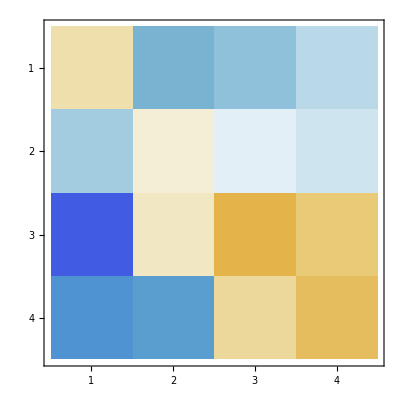

```mathematica
H2=-Inverse[P2].Q2;
MatrixPlot[H2]
```

```mathematica
{EE2,ψψ2}=Eigensystem[N[H2,16]];
EE2
ψψ2
```

{105.3290788081472,38.23153880351976,7.276073636650283,-0.9999965486040098}

{{0.02853516577258507,0.002178220711960531,-0.8896632977766127,-0.4557194490671901},{-0.02766277968533142,0.009496039558670709,0.7754785749900799,-0.630696103986806},{-0.1812122709492607,0.05433707878616166,-0.9709011212512384,0.1468353073326924},{0.2646535020748803,0.3211234261220093,0.8695732909299655,0.2658581590555259}}

```mathematica
(* This cell requires 2024.05.02 ContEvol H failure.nb *)
(* ψ2=normalN[ψψ2[[-1]],2]*ψψ2[[-1]];
Plot[{ψexact[r],renderN[ψ2,2,r]},{r,0,2}] *)
```

```mathematica
(* 2024.05.01 ContEvol H derivation.nb *)
```

```mathematica
ϕe[r_]:=D r+C r^2+B r^3+A r^4;
ϕdote[r_]:=D+2 C r+3 B r^2+4 A r^3;
```

```mathematica
{ψA,ψB,ψC,ψD}={ψdot0/(h^3 i)+(-ψ0+3 i^2 ψ0+2 i^3 ψ0-3 i^2 ψh-2 i^3 ψh)/(h^4 i^2 (1+i)^2),(-2 ψdot0-3 i ψdot0)/(h^2 i)+(2 ψ0+4 i ψ0-4 i^2 ψ0-12 i^3 ψ0-6 i^4 ψ0+4 i^2 ψh+12 i^3 ψh+6 i^4 ψh)/(h^3 i^2 (1+i)^2),((1+i) (ψdot0+3 i ψdot0))/(h i)+(-ψ0-6 i ψ0-6 i^2 ψ0+8 i^3 ψ0+15 i^4 ψ0+6 i^5 ψ0-8 i^3 ψh-15 i^4 ψh-6 i^5 ψh)/(h^2 i^2 (1+i)^2),-(1+i)^2 ψdot0+(2 ψ0+4 i ψ0-4 i^3 ψ0-2 i^4 ψ0+4 i^3 ψh+2 i^4 ψh)/(h i (1+i))};
```

```mathematica
{ϕA,ϕB,ϕC,ϕD}={ϕdot0/(h^3 i)+(-ϕ0+3 i^2 ϕ0+2 i^3 ϕ0-3 i^2 ϕh-2 i^3 ϕh)/(h^4 i^2 (1+i)^2),(-2 ϕdot0-3 i ϕdot0)/(h^2 i)+(2 ϕ0+4 i ϕ0-4 i^2 ϕ0-12 i^3 ϕ0-6 i^4 ϕ0+4 i^2 ϕh+12 i^3 ϕh+6 i^4 ϕh)/(h^3 i^2 (1+i)^2),((1+i) (ϕdot0+3 i ϕdot0))/(h i)+(-ϕ0-6 i ϕ0-6 i^2 ϕ0+8 i^3 ϕ0+15 i^4 ϕ0+6 i^5 ϕ0-8 i^3 ϕh-15 i^4 ϕh-6 i^5 ϕh)/(h^2 i^2 (1+i)^2),-(1+i)^2 ϕdot0+(2 ϕ0+4 i ϕ0-4 i^3 ϕ0-2 i^4 ϕ0+4 i^3 ϕh+2 i^4 ϕh)/(h i (1+i))};
```

```mathematica
(* t: tail, actually i=N-1 here *)
ψψt[r_]:=ψD r+ψC r^2+ψB r^3+ψA r^4;
ϕϕt[r_]:=ϕD r+ϕC r^2+ϕB r^3+ϕA r^4;
```

```mathematica
(* Integrate[Simplify[∂_r ∂_r ψψt[r]+2ψψt[r]/r+ϕϕt[r]]^2,{r,i h,(i+1)h}] *)
ϵt[ψ0_,ψh_,ψdot0_,ϕ0_,ϕh_,ϕdot0_]:=1/(1260 h^3 i^4 (1+i)^4)(h^6 i^2 (1+i)^4 (2+9 i+12 i^2) ϕdot0^2+h^5 i (1+i)^2 ϕdot0 ((1+i)^2 (-4-i+60 i^2+132 i^3) ϕ0+i (78 i^4 ϕh+18 ψdot0+12 i^3 (15 ϕh+4 ψdot0)+6 i (5 ϕh+14 ψdot0)+i^2 (127 ϕh+114 ψdot0)))+1008 ((1+i)^4 (1-4 i+4 i^2+15 i^4) ψ0^2-2 i^2 (1+i)^2 (-3+4 i+19 i^2+30 i^3+15 i^4) ψ0 ψh+i^4 (24+72 i+94 i^2+60 i^3+15 i^4) ψh^2)-168 h ((1+i)^4 (1-2 i-3 i^2+36 i^3) ψ0^2+i^3 ψh (6 (1+i)^2 (6+19 i+30 i^2+15 i^3) ψdot0+i (36+112 i+111 i^2+36 i^3) ψh)-i (1+i)^2 ψ0 (6 (1+i)^2 (-2+4 i+15 i^3) ψdot0+i (-5+26 i+108 i^2+72 i^3) ψh))-24 h^2 (-2 ψ0^2+14 i ψ0 (ψ0-ψdot0)-42 i^8 (5 ψdot0^2+3 ϕh (ψ0-ψh))+2 (1+i)^2 ϕ0 ((1+i)^2 (1-4 i+4 i^2+63 i^4) ψ0-i^2 (-3+4 i+67 i^2+126 i^3+63 i^4) ψh)+2 i^2 (3 ϕh ψ0-ψ0^2-35 ψ0 ψdot0-21 ψdot0^2+8 ψ0 ψh)-2 i^6 (39 ψ0^2-497 ψ0 ψdot0+651 ψdot0^2+382 ϕh (ψ0-ψh)+27 ψ0 ψh+77 ψdot0 ψh+39 ψh^2)-2 i^4 (191 ψ0^2-434 ψ0 ψdot0+231 ψdot0^2+72 ϕh (ψ0-ψh)+73 ψ0 ψh+70 ψdot0 ψh+51 ψh^2)-i^5 (290 ψ0^2-1442 ψ0 ψdot0+1008 ψdot0^2+528 ϕh (ψ0-ψh)+162 ψ0 ψh+217 ψdot0 ψh+178 ψh^2)-42 i^7 (12 ϕh (ψ0-ψh)+ψdot0 (-6 ψ0+20 ψdot0+ψh))+i^3 (4 ϕh ψ0-188 ψ0^2+2 ψ0 (56 ψdot0-11 ψh)-7 ψdot0 (24 ψdot0+5 ψh)))+6 h^3 ((1+i)^2 ϕ0 ((1+i)^2 (3-20 i-16 i^2+312 i^3) ψ0+i (-2 (1+i)^2 (-4+i+14 i^2+231 i^3) ψdot0+i (-17+20 i+162 i^2+108 i^3) ψh))+i (42 i^7 ϕh ψdot0-16 ψ0 ψdot0+i (-17 ϕh ψ0+4 (6 ψ0-7 ψdot0) ψdot0)-2 (1+i)^2 ϕdot0 ((1+i)^2 (-4+i+14 i^2+21 i^3) ψ0-i^2 (12+50 i+56 i^2+21 i^3) ψh)+i^2 (ϕh (-14 ψ0+24 ψdot0)+32 ψdot0 (8 ψ0-7 ψdot0+2 ψh))+4 i^6 (-28 ψdot0^2+ϕh (27 ψ0+49 ψdot0+78 ψh))+4 i^4 (14 ψdot0 (6 ψ0-14 ψdot0+3 ψh)+ϕh (113 ψ0+84 ψdot0+237 ψh))+i^3 (4 ψdot0 (116 ψ0-154 ψdot0+45 ψh)+ϕh (185 ψ0+148 ψdot0+305 ψh))+i^5 (4 ψdot0 (22 ψ0-119 ψdot0+13 ψh)+ϕh (378 ψ0+366 ψdot0+952 ψh))))+2 h^4 ((1+i)^4 (1-4 i-17 i^2+42 i^3+234 i^4) ϕ0^2+i (1+i)^2 ϕ0 (-15 i ϕh+162 i^5 ϕh-9 ψdot0+12 i^4 (27 ϕh+11 ψdot0)+2 i^3 (77 ϕh+141 ψdot0)+i^2 (-8 ϕh+159 ψdot0))+i (-9 ϕdot0 ψ0+6 i^7 (39 ϕh^2-28 ϕdot0 ψdot0)-6 i (3 ϕdot0 ψ0+4 ϕdot0 ψdot0-4 ψdot0^2)+12 i^3 (15 ϕh^2+50 ϕdot0 ψ0-54 ϕdot0 ψdot0+20 ϕh ψdot0+12 ψdot0^2+20 ϕdot0 ψh)+3 i^4 (260 ϕh^2+285 ϕdot0 ψ0-424 ϕdot0 ψdot0+135 ϕh ψdot0+32 ψdot0^2+135 ϕdot0 ψh)+6 i^6 (149 ϕh^2+13 ϕh ψdot0+ϕdot0 (22 ψ0-126 ψdot0+13 ψh))+3 i^2 (ψdot0 (17 ϕh+32 ψdot0)+ϕdot0 (50 ψ0-60 ψdot0+17 ψh))+i^5 (1261 ϕh^2+294 ϕh ψdot0+6 (91 ϕdot0 ψ0-228 ϕdot0 ψdot0+4 ψdot0^2+49 ϕdot0 ψh)))));
```

```mathematica
D[ϵt[ψ0,ψh,ψdot0,ϕ0,ϕh,ϕdot0], ϕ0]
```

1/(1260 h^3 i^4 (1+i)^4)(h^5 i (1+i)^4 (-4-i+60 i^2+132 i^3) ϕdot0+2 h^4 (2 (1+i)^4 (1-4 i-17 i^2+42 i^3+234 i^4) ϕ0+i (1+i)^2 (-15 i ϕh+162 i^5 ϕh-9 ψdot0+12 i^4 (27 ϕh+11 ψdot0)+2 i^3 (77 ϕh+141 ψdot0)+i^2 (-8 ϕh+159 ψdot0)))-48 h^2 (1+i)^2 ((1+i)^2 (1-4 i+4 i^2+63 i^4) ψ0-i^2 (-3+4 i+67 i^2+126 i^3+63 i^4) ψh)+6 h^3 (1+i)^2 ((1+i)^2 (3-20 i-16 i^2+312 i^3) ψ0+i (-2 (1+i)^2 (-4+i+14 i^2+231 i^3) ψdot0+i (-17+20 i+162 i^2+108 i^3) ψh)))

```mathematica
D[ϵt[ψ0,ψh,ψdot0,ϕ0,ϕh,ϕdot0], ϕh]
```

1/(1260 h^3 i^4 (1+i)^4)(h^5 i^2 (1+i)^2 (30 i+127 i^2+180 i^3+78 i^4) ϕdot0+2 h^4 (i (1+i)^2 (-15 i-8 i^2+154 i^3+324 i^4+162 i^5) ϕ0+i (468 i^7 ϕh+51 i^2 ψdot0+6 i^6 (298 ϕh+13 ψdot0)+12 i^3 (30 ϕh+20 ψdot0)+3 i^4 (520 ϕh+135 ψdot0)+i^5 (2522 ϕh+294 ψdot0)))-24 h^2 (6 i^2 ψ0+4 i^3 ψ0-144 i^4 (ψ0-ψh)-528 i^5 (ψ0-ψh)-764 i^6 (ψ0-ψh)-504 i^7 (ψ0-ψh)-126 i^8 (ψ0-ψh))+6 h^3 i (-17 i ψ0+42 i^7 ψdot0+i^2 (-14 ψ0+24 ψdot0)+4 i^6 (27 ψ0+49 ψdot0+78 ψh)+4 i^4 (113 ψ0+84 ψdot0+237 ψh)+i^3 (185 ψ0+148 ψdot0+305 ψh)+i^5 (378 ψ0+366 ψdot0+952 ψh)))

```mathematica
D[ϵt[ψ0,ψh,ψdot0,ϕ0,ϕh,ϕdot0], ϕdot0]
```

1/(1260 h^3 i^4 (1+i)^4)(2 h^6 i^2 (1+i)^4 (2+9 i+12 i^2) ϕdot0+h^5 i (1+i)^2 ((1+i)^2 (-4-i+60 i^2+132 i^3) ϕ0+i (78 i^4 ϕh+18 ψdot0+12 i^3 (15 ϕh+4 ψdot0)+6 i (5 ϕh+14 ψdot0)+i^2 (127 ϕh+114 ψdot0)))-12 h^3 i (1+i)^2 ((1+i)^2 (-4+i+14 i^2+21 i^3) ψ0-i^2 (12+50 i+56 i^2+21 i^3) ψh)+2 h^4 i (-9 ψ0-168 i^7 ψdot0-6 i (3 ψ0+4 ψdot0)+6 i^6 (22 ψ0-126 ψdot0+13 ψh)+3 i^2 (50 ψ0-60 ψdot0+17 ψh)+12 i^3 (50 ψ0-54 ψdot0+20 ψh)+6 i^5 (91 ψ0-228 ψdot0+49 ψh)+3 i^4 (285 ψ0-424 ψdot0+135 ψh)))

```mathematica
Ptmat[i_,h_]:={{(h (1-4 i-17 i^2+42 i^3+234 i^4))/(315 i^4),(h (-15 i-8 i^2+154 i^3+324 i^4+162 i^5))/(630 i^3 (1+i)^2),(h^2 (-4-i+60 i^2+132 i^3))/(1260 i^3)},
{(h (-15 i-8 i^2+154 i^3+324 i^4+162 i^5))/(630 i^3 (1+i)^2),(h (360 i^3+1560 i^4+2522 i^5+1788 i^6+468 i^7))/(630 i^3 (1+i)^4),(h^2 (30 i+127 i^2+180 i^3+78 i^4))/(1260 i^2 (1+i)^2)},
{(h^2 (-4-i+60 i^2+132 i^3))/(1260 i^3),(h^2 (30 i+127 i^2+180 i^3+78 i^4))/(1260 i^2 (1+i)^2),(h^3 (2+9 i+12 i^2))/(630 i^2)}}
```

```mathematica
Simplify[D[D[ϵt[ψ0,ψh,ψdot0,ϕ0,ϕh,ϕdot0], ϕ0], ψdot0]]
```

(h (-3+6 i+44 i^2)-2 (-4+i+14 i^2+231 i^3))/(210 i^3)

```mathematica
Qtmat[i_,h_]:={{(h (3-20 i-16 i^2+312 i^3)-8 (1-4 i+4 i^2+63 i^4))/(210 h i^4),(h (-17+20 i+162 i^2+108 i^3)+8 (-3+4 i+67 i^2+126 i^3+63 i^4))/(210 h i^2 (1+i)^2),(h (-3+6 i+44 i^2)-2 (-4+i+14 i^2+231 i^3))/(210 i^3)},
{(h (-17+20 i+162 i^2+108 i^3)+8 (-3+4 i+67 i^2+126 i^3+63 i^4))/(210 h i^2 (1+i)^2),(h (305+948 i+952 i^2+312 i^3)-8 (72+264 i+382 i^2+252 i^3+63 i^4))/(210 h (1+i)^4),(h (17+46 i+26 i^2)+2 (12+50 i+56 i^2+21 i^3))/(210 i (1+i)^2)},
{(h (-3+6 i+44 i^2)-2 (-4+i+14 i^2+21 i^3))/(210 i^3),(h (17+46 i+26 i^2)+2 (12+50 i+56 i^2+21 i^3))/(210 i (1+i)^2),(h (h (3+8 i)-4 (2+7 i+14 i^2)))/(210 i^2)}}
```

```mathematica
Ptmat[1,1/2]
```

{{128/315,617/5040,187/5040},{617/5040,3349/10080,83/4032},{187/5040,83/4032,23/5040}}

```mathematica
Ptrial=ConstantArray[0,{4,4}];
Tmat0=T0mat[1/2];Pbar0=Pbar[0,1/2][[{2,3,4},{2,3,4}]];
Ptrial[[{1,3,4},{1,3,4}]]+=Transpose[Tmat0].Pbar0.Tmat0;
Ptrial[[{1,2,4},{1,2,4}]]+=Ptmat[1,1/2];
Ptrial[[2,2]]+=5/2;
Ptrial-P2
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Qtmat[1,1/2]
```

{{-149/42,877/168,-307/140},{877/168,-14011/3360,43/112},{-27/140,43/112,-173/840}}

```mathematica
Qtrial=ConstantArray[0,{4,4}];
Tmat0=T0mat[1/2];Qbar0=Qbar[0,1/2][[{2,3,4},{2,3,4}]];
Qtrial[[{1,3,4},{1,3,4}]]+=Transpose[Tmat0].Qbar0.Tmat0;
Qtrial[[{1,2,4},{1,2,4}]]+=Qtmat[1,1/2];
Qtrial[[2,2]]+=5/2;
Qtrial-Q2
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}